```mathematica
a[xi_,eta_]:=3xi/(2-Sqrt[3]eta)
b[xi_,eta_]:=(2Sqrt[3]eta-1)/3
domain=Triangle[{{-1,-Sqrt[3]/3},{1,-Sqrt[3]/3},{0,2Sqrt[3]/3}}];
D[a[x,y],x]
D[a[x,y],y]
D[b[x,y],x]
D[b[x,y],y]
```

3/(2-√3 y)

(3 √3 x)/(2-√3 y)^2

0

2/(√3)

```mathematica
f[r_,s_]:=r*s+s+4r^2
Integrate[f[x,y],x,y]
Integrate[f[a[x,y],b[x,y]],x,y]
```

(4 x^3 y)/3+(x y^2)/2+(x^2 y^2)/4

1/6 x (-2 (1+3 x) y+2 √3 y^2-(24 √3 x^2)/(-2+√3 y)-3 √3 x Log[-2+√3 y])

```mathematica
Integrate[f[x,y],{x,-1,1},{y,-1,1}]
Integrate[f[a[x,y],b[x,y]],{x,y}∈domain]
```

16/3

√3

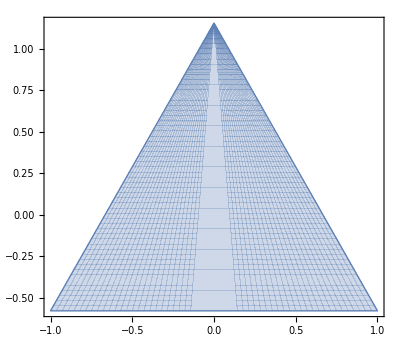
{-Graphics-,-Graphics-}

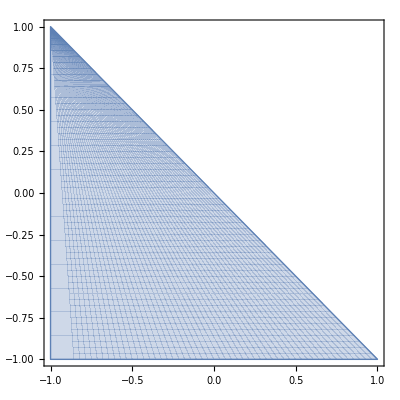
{-Graphics-,-Graphics-}

```mathematica
{ParametricPlot[{a[r,s],b[r,s]},{r,s}∈Triangle[{{-1,-1/Sqrt[3]},{1,-1/Sqrt[3]},{0,2/Sqrt[3]}}]],ParametricPlot[{a((3-3b)/2)/3,(3b+1)/(2Sqrt[3])},{a,-1,1},{b,-1,1}]}
{ParametricPlot[{2(r+1)/(1-s)-1,s},{r,s}∈Triangle[{{-1,-1},{1,-1},{-1,1}}]],ParametricPlot[{((a+1)*(1-b))/2-1,b},{a,-1,1},{b,-1,1}]}
```